```mathematica
ExportPath=".";
skip=20;
du=dv=1/100;
massReduct=1/1000;
v1= 0;
m0=1;
Q0=8/10;
SourcesRParam =1;
SourcesRParamR =1;
SourcesSParam = 1;
SourcesSParamR =1;
SourcesS5Param =0;
deltaUV5Param = 70;
QuvFactor =1;
Qreduct=Q0/m0*massReduct;
deltav =900;
v2 =v1+deltav;
RStarConst =-30;
Vvec = Table[v,{v,v1,v2,dv}];
MFunc = (m0^3-(v-v1)*massReduct)^(1/3);
QFunc = MFunc * Q0;
Clear[pdesolskip,RTable,STable,RvTable,RvvTable,RuTable,RuuTable,SvTable,SvvTable,SuTable,SuuTable];
Uvec = 2*RStarConst- Vvec;
Uvec0=Table[u,{u,Uvec[[-1]],Uvec[[1]],du}];
UvecSkipped = Uvec0[[1;;-1;;skip]];
VvecSkipped = Vvec[[1;;-1;;skip]];
deltaUV5 = (Uvec0[[1]]+Vvec[[1]])/2+deltaUV5Param; 
vsol=DSolve[{H'[v]==κp/.{Q->QFunc,m->MFunc},H[0]==0},H[v],{v,v1,v2}(*,Method->"StiffnessSwitching",WorkingPrecision->60*)];
vtilde=(H[v]/.vsol/.{v->Vvec})[[1]];
usol=DSolve[{H'[u]==κp/.{Q->(QFunc/.v->-u),m->(MFunc/.v->-u)},H[0]==0},H[u],u(*,{u,Uvec[[1]],Uvec[[-1]]},Method->"StiffnessSwitching",WorkingPrecision->60*)];
utilde=(H[u]/.usol/.{u->Uvec})[[1]];
Ttilde=(utilde+vtilde)/2;
MTable= MFunc/.{v->Vvec}//N100;
QTable = QFunc/.{v->Vvec}//N100;
QuvTable = QuvFactor *massReduct* MTable^-1 ;
QuvScale=MTable^-1;
MuTable = MFunc /. {v->-Uvec}//N100;
QuTable = QFunc /. {v->-Uvec}//N100;
κpu=(κp/.{m->μ,Q->Qu});
sInitFixed = Log[-r *f/2]+Log[κpu]-Log[κp];
DRDUFixed=r f *κpu/κp;
DLogκpuDu=D[Log[κpu],μ]*D[(MFunc/.v->-u),u]+D[Log[κpu],Qu]*D[(QFunc/.v->-u),u];
DSDUFixed=D[Log[-r f ],r] *DRDUFixed/(2r)+DLogκpuDu;
SourcesR=massReduct*SourcesRParam/MTable^3;
SourcesS = massReduct*SourcesSParam/MTable^5;
SourcesRR =massReduct* SourcesRParamR/MTable^4;
SourcesRS = massReduct*SourcesSParamR/MTable^6;
SourcesR5=0*Vvec;
SourcesS5 = massReduct*SourcesS5Param*MTable;
time0=AbsoluteTiming[
RStarVector=Table[ (Ttilde[[j]]/κp/.{m->MTable[[j]],Q->QTable[[j]]}),{j,1,Length[MTable]}];
rInit=Table[RFromRStar[RStarVector[[j]],MTable[[j]],QTable[[j]]],{j,1,Length[MTable]}];
RInitVector = Table[ rInit[[j]]^2,{j,1,Length[MTable]}];
SInitVector =  Table[ (sInitFixed/.{m->MTable[[j]],μ->MuTable[[j]],r->rInit[[j]],Q->QTable[[j]],Qu->QuTable[[j]]})//N,{j,1,Length[MTable]}];
DRInitVector =  Table[ (DRDUFixed/.{m->MTable[[j]],μ->MuTable[[j]],r->rInit[[j]],Q->QTable[[j]],Qu->QuTable[[j]]})//N,{j,1,Length[MTable]}];
DSInitVector =  Table[ (DSDUFixed/.{m->MTable[[j]],μ->MuTable[[j]],u->Uvec[[j]],r->rInit[[j]],Q->QTable[[j]],Qu->QuTable[[j]]})//N,{j,1,Length[MTable]}];
midpointDR = (DRInitVector[[2;;]]+DRInitVector[[;;-2]])/2;
midpointDS = (DSInitVector[[2;;]]+DSInitVector[[;;-2]])/2;
{Ruv,Suv}=ComputeRuvSuvQuvScale[RInitVector,SInitVector,(QTable[[2;;]]+QTable[[;;-2]])/2,SourcesR,SourcesS,QuvTable,Uvec0[[1]]+Vvec[[1]],QuvScale, dv,SourcesRR,SourcesRS,SourcesR5,SourcesS5,deltaUV5];
R2InitVector=RInitVector[[2;;]]+du*(midpointDR+1/2*dv*Ruv);
S2InitVector=SInitVector[[2;;]]+du*(midpointDS+1/2*dv*Suv);]
time2=AbsoluteTiming[pdesolskip=pyPdeSolveQuvScale[skip,R2InitVector,RInitVector,S2InitVector,SInitVector,(QTable//N),(du//N),(dv//N),SourcesR//N,SourcesS//N,QuvTable//N,(Uvec0[[1]]+Vvec[[1]])//N, QuvScale // N,SourcesRR//N,SourcesRS//N,SourcesR5 // N,SourcesS5//N,deltaUV5//N];]
(* R,S,Rv,Rvv,Ru,Ruu,Sv,Svv,Su,Suu *)
RTable = Normal[pdesolskip[[1]]];
STable = Normal[pdesolskip[[2]]];
RvTable = Normal[pdesolskip[[3]]];
RvvTable = Normal[pdesolskip[[4]]];
RuTable = Normal[pdesolskip[[5]]];
RuuTable = Normal[pdesolskip[[6]]];
SvTable = Normal[pdesolskip[[7]]];
SvvTable = Normal[pdesolskip[[8]]];
SuTable = Normal[pdesolskip[[9]]];
SuuTable = Normal[pdesolskip[[10]]];
cu = RuTable*SuTable-RuuTable;
cv = RvTable*SvTable-RvvTable;
cuv = cu-cv;
```

{101.479,Null}

10% Done

20% Done

30% Done

40% Done

50% Done

60% Done

70% Done

80% Done

90% Done

100% Done

Done calculating

{160.116,Null}

```mathematica
RTables[massReduct] = RTable;
STables[massReduct] = STable;
RvTables[massReduct] = RvTable;
RvvTables[massReduct] = RvvTable;
RuTables[massReduct] = RuTable;
RuuTables[massReduct] = RuuTable;
SvTables[massReduct] = SvTable;
SvvTables[massReduct] = SvvTable;
SuTables[massReduct] = SuTable;
SuuTables[massReduct] = SuuTable;
cus[massReduct]=cu;
cvs[massReduct]=cv;
MTables[massReduct] = MTable;
QTables[massReduct] = QTable;
MFuncs[massReduct]=MFunc;
QFuncs[massReduct]=QFunc;
UvecSkippeds[massReduct]=UvecSkipped;

RTables[dv] = RTable;
STables[dv] = STable;
RvTables[dv] = RvTable;
RvvTables[dv] = RvvTable;
RuTables[dv] = RuTable;
RuuTables[dv] = RuuTable;
SvTables[dv] = SvTable;
SvvTables[dv] = SvvTable;
SuTables[dv] = SuTable;
SuuTables[dv] = SuuTable;
cus[dv]=cu;
cvs[dv]=cv;

RTables[RStarConst] = RTable;
STables[RStarConst] = STable;
RvTables[RStarConst] = RvTable;
RvvTables[RStarConst] = RvvTable;
RuTables[RStarConst] = RuTable;
RuuTables[RStarConst] = RuuTable;
SvTables[RStarConst] = SvTable;
SvvTables[RStarConst] = SvvTable;
SuTables[RStarConst] = SuTable;
SuuTables[RStarConst] = SuuTable;
cus[RStarConst]=cu;
cvs[RStarConst]=cv;
UvecSkippeds[RStarConst]=UvecSkipped;
DumpSave["current_run.mx",{RTable,STable,RvTable,RvvTable,RuTable,RuuTable,SvTable,SvvTable,SuTable,SuuTable,MTable,QTable,VvecSkipped,UvecSkipped,MFunc,QFunc,du,dv,skip,massReduct,RStarConst,SourcesRParam ,SourcesRParamR,SourcesSParam ,SourcesSParamR ,SourcesS5Param ,deltaUV5Param ,QuvFactor,cu,cv}];
```

```mathematica
DumpGet["current_run.mx"]
```

```mathematica
(RTables[1/50][[-1,-1]]-RTables[1/100][[-1,-1]])/(RTables[1/100][[-1,-1]]-RTables[1/200][[-1,-1]])
```

4.00055

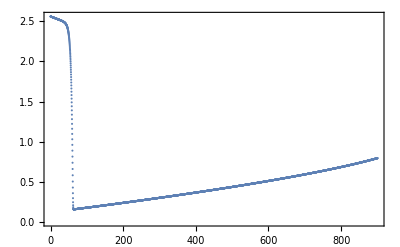

```mathematica
ExportAndShow["R(v)",ListPlot[{VvecSkipped,RTable[[;;,-1]]}//Transpose,PlotRange->All,Frame->True,FrameLabel->MaTeX/@{"v","R(v,u=-60)"}]]
```

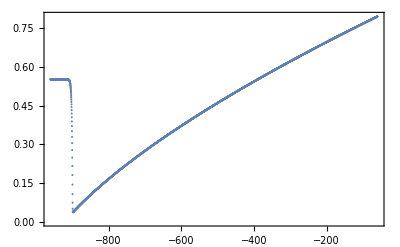

```mathematica
ExportAndShow["R(u)",ListPlot[{UvecSkipped,RTable[[-1,;;]]}//Transpose,PlotRange->All,Frame->True,FrameLabel->MaTeX/@{"u","R(v=900,u)"}]]
```

```mathematica
TvvInitial = (2D[MFunc,v]-2D[QFunc,v]QFunc/(rp/.{m->MFunc,Q->QFunc}));
```

```mathematica
(* Tuu(v,u=const)*)
```

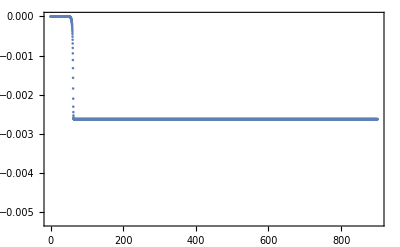
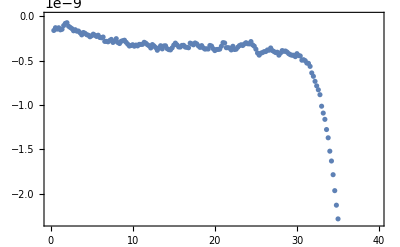

```mathematica
{ExportAndShow["Tuu(v)",ListPlot[{VvecSkipped[[2;;]],cu[[2;;,-2]]}//Transpose,Frame->True,FrameLabel->{MaTeX@"v",Rotate[MaTeX@"\\widetilde{T}_{uu}",-90 Degree]}]],ExportAndShow["Tuu(v upto 40)",ListPlot[{VvecSkipped[[2;;200]],cu[[2;;200,-2]]}//Transpose,Frame->True,FrameLabel->{MaTeX@"v",Rotate[MaTeX@"\\widetilde{T}_{uu}",-90 Degree]}]]}
```

```mathematica
(*Tuu(v=const,u)*)
```

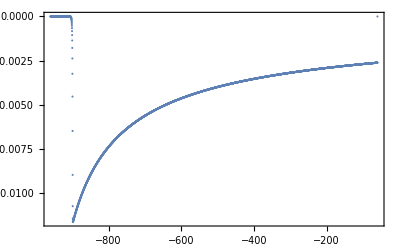
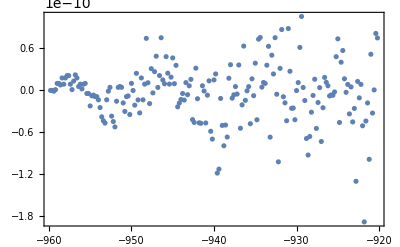

```mathematica
{ExportAndShow["Tuu(u)",ListPlot[{UvecSkipped[[2;;]],cu[[-1,2;;]]}//Transpose,PlotRange->All,Frame->True,FrameLabel->{MaTeX@"u",Rotate[MaTeX@"\\widetilde{T}_{uu}",-90 Degree]}]],ExportAndShow["Tuu(u upto 40)",ListPlot[{UvecSkipped[[2;;200]],cu[[-1,2;;200]]}//Transpose,PlotRange->All,Frame->True,FrameLabel->{MaTeX@"u",Rotate[MaTeX@"\\widetilde{T}_{uu}",-90 Degree]}]]}
```

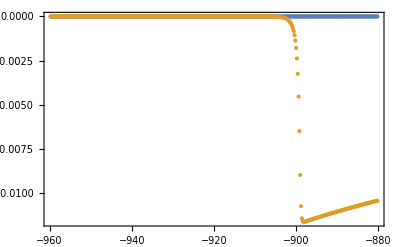

```mathematica
ListPlot[{{UvecSkipped[[2;;400]],cu[[-1,2;;400]]*0}//Transpose,{UvecSkipped[[2;;400]],cu[[-1,2;;400]]}//Transpose},PlotRange->All,Frame->True,FrameLabel->{MaTeX@"u",Rotate[MaTeX@"\\widetilde{T}_{uu}",-90 Degree]}]
```

```mathematica
(* Tvv(v,u=const), and analytical expression for Tvv*)
```

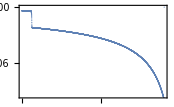

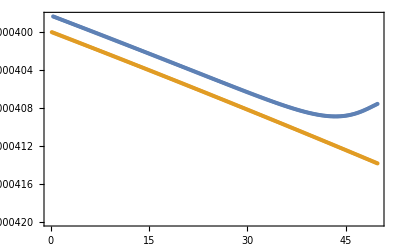

```mathematica
ExportAndShow["Tvv(v)",ListPlot[{VvecSkipped[[2;;]],cv[[2;;,-2]]}//Transpose,Frame->True,FrameLabel->{MaTeX@"v",Rotate[MaTeX@"\\widetilde{T}_{vv}",-90 Degree]}]]
ExportAndShow["Tvv(v upto 50)",ListPlot[{{VvecSkipped[[2;;250]],Table[cv[[j,-2]],{j,2,250}]}//Transpose,{VvecSkipped[[2;;250]],Table[TvvInitial/.{v->Vvec[[(j-1)*skip+1]]},{j,2,250}]}//Transpose},Frame->True,FrameLabel->{MaTeX@"v",Rotate[MaTeX@"\\widetilde{T}_{vv}",-90 Degree]},PlotLegends->Placed[MaTeX/@{"\\widetilde{T}_{vv}","2M_{,v}-\\frac{2QQ_{,v}}{r}"}, Top]]]
```

```mathematica
(*Tvv(v=const, u)*)
```

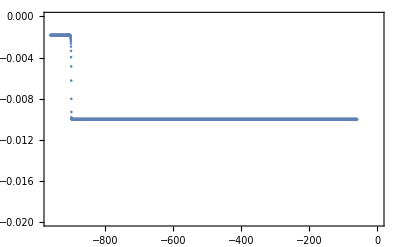
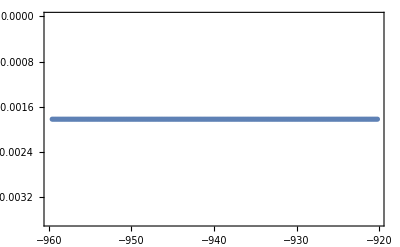

```mathematica
{ExportAndShow["Tvv(u)",ListPlot[{UvecSkipped[[2;;]],cv[[-2,2;;]]}//Transpose,Frame->True,FrameLabel->{MaTeX@"u",Rotate[MaTeX@"\\widetilde{T}_{vv}",-90 Degree]}]],ExportAndShow["Tvv(u upto 40)",ListPlot[{UvecSkipped[[2;;200]],cv[[-2,2;;200]]}//Transpose,Frame->True,FrameLabel->{MaTeX@"u",Rotate[MaTeX@"\\widetilde{T}_{vv}",-90 Degree]}]]}
```

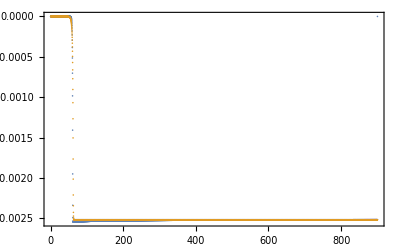

```mathematica
(*
R Tuu Mu^2:
Blue: v=const, u varies
Orange: u=const, v varies
Note: x axis isn't correct for Blue.
*)
ExportAndShow["Tuu Mu^2",ListPlot[{{VvecSkipped[[2;;]],cu[[-1,2;;]]*(MFunc/.{v->-Uvec0[[1*skip+1;;-1;;skip]]})^2}//Transpose,{VvecSkipped[[3;;]],cu[[3;;,-2]]*(MFunc/.{v->-Uvec0[[-2]]})^2}//Transpose},PlotRange->All,Frame->True,FrameLabel->{MaTeX@"v\; or\; u",Rotate[MaTeX@"\\widetilde{T}_{uu}M^u(u)^2",-90 Degree]}]]
```

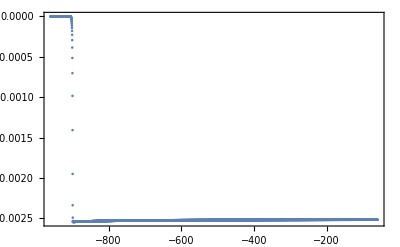

```mathematica
ExportAndShow["Tuu(u) Mu^2",ListPlot[{UvecSkipped[[2;;-2]],cu[[-1,2;;-2]]*(MFunc/.{v->-Uvec0[[1*skip+1;;-1-skip;;skip]]})^2}//Transpose,PlotRange->All,Frame->True,FrameLabel->{MaTeX@"u",Rotate[MaTeX@"\\widetilde{T}_{uu}M^u(u)^2",-90 Degree]}]]
```

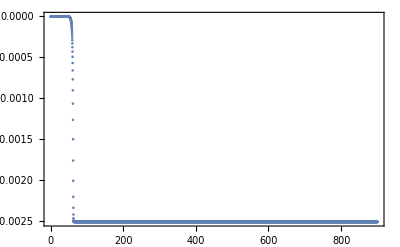

```mathematica
ExportAndShow["Tuu(v) Mu^2",ListPlot[{VvecSkipped[[3;;]],cu[[3;;,-2]]*(MFunc/.{v->-Uvec0[[-2]]})^2}//Transpose,PlotRange->All,Frame->True,FrameLabel->{MaTeX@"v",Rotate[MaTeX@"\\widetilde{T}_{uu}M^u(u)^2",-90 Degree]}]]
```

```mathematica
(*
R Tvv Mv^2:
Blue: u=const, v varies
Orange: v=const, u varies
Note: X axis isn't correct for Orange.
*)
```

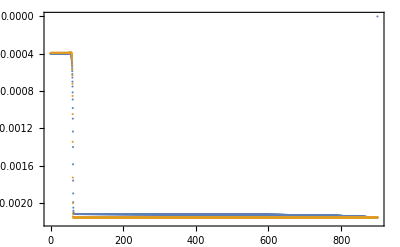

```mathematica
ExportAndShow["Tvv(v) M^2",ListPlot[{{VvecSkipped[[2;;]],cv[[2;;,-1]]*MTable[[2;;-1;;skip]]^2}//Transpose,{VvecSkipped[[2;;]],cv[[-2,2;;]]*MTable[[-2]]^2}//Transpose},Frame->True,FrameLabel->{MaTeX@"v\; or\; u",Rotate[MaTeX@"\\widetilde{T}_{vv}M^v(v)^2",-90 Degree]}]]
```

```mathematica
(*Region 1*)
```

```mathematica
(* Tvv and analytical expression along the initial conditions*)
```

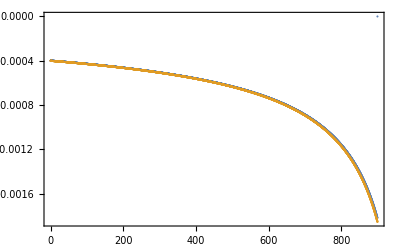

```mathematica
TvvInitial = (2D[MFunc,v]-2D[QFunc,v]QFunc/r);
ExportAndShow["Tvv(initial value)",ListPlot[{{VvecSkipped[[2;;-2]],Table[cv[[j+1,-j]],{j,2,Length[cv]-1}]}//Transpose,{VvecSkipped[[2;;-2]],Table[TvvInitial/.{v->Vvec[[(j-1)*skip+1]],r->Sqrt[RTable[[j+1,-j]]]},{j,2,Length[cv]-1}]}//Transpose},Frame->True,FrameLabel->{MaTeX@"v",Rotate[MaTeX@"\\widetilde{T}_{vv}",-90 Degree]},PlotLegends->Placed[MaTeX/@{"\\widetilde{T}_{vv}","2M_{,v}-\\frac{2QQ_{,v}}{r}"}, Top]]]
```

```mathematica
(* Scaling of Tvv: Tvv * M^2*)
```

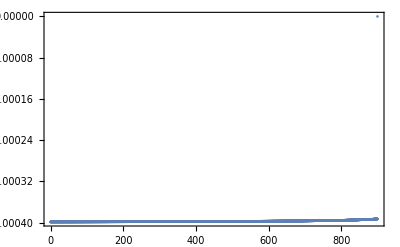

```mathematica
ExportAndShow["Tvv(initial values) M^2",ListPlot[{VvecSkipped[[2;;-2]],Table[cv[[j+1,-j]]*MTable[[(j-1)*skip+1]]^2,{j,2,Length[cv]-1}]}//Transpose,Frame->True,FrameLabel->{MaTeX@"v",Rotate[MaTeX@"\\widetilde{T}_{vv}M(v)^2",-90 Degree]}]]
```

```mathematica
(* Tuu along initial conditions *)
```

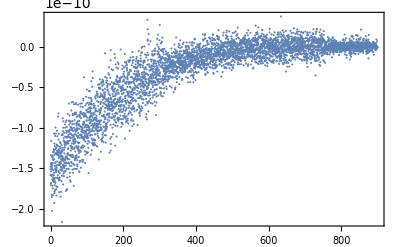

```mathematica
ExportAndShow["Tuu(initial values)",ListPlot[{VvecSkipped[[2;;-2]],Table[cu[[j+1,-j]],{j,2,Length[cv]-1}]}//Transpose,Frame->True,FrameLabel->{MaTeX@"v",Rotate[MaTeX@"\\widetilde{T}_{uu}",-90 Degree]}]]
```

```mathematica
(* Tvv-analytical expression along initial conditions*)
```

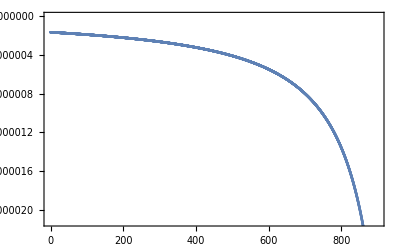

```mathematica
ExportAndShow["Tvv(v)-Analytical Expr",ListPlot[{VvecSkipped[[1;;-2]],Table[-cv[[j+1,-j]]+TvvInitial/.{v->Vvec[[(j-1)*skip+1]],r->Sqrt[RTable[[j+1,-j]]]},{j,1,Length[cv]-1}]}//Transpose,Frame->True,FrameLabel->{MaTeX@"v",MaTeX@"\\widetilde{T}_{vv}-2M_{,v}+\\frac{2QQ_{,v}}{r}"}]]
```

```mathematica
(*Region 2*)
```

```mathematica
(* R of RN (at certain v) versus computed R *)
```

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of FindRoot::cvmit will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than 50. digits of working precision to meet these tolerances.

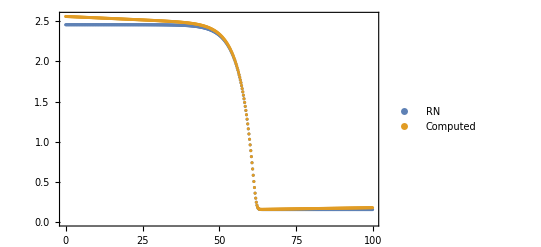

```mathematica
RNRTableU=Table[RFromRStar[(Uvec0[[-1]]+Vvec[[j]])/2,MFunc/.{v->-Uvec0[[-1]]},QFunc/.{v->-Uvec0[[-1]]}]^2,{j,1,500*skip,skip}];
ExportAndShow["R(v) RN",ListPlot[{{VvecSkipped[[1;;500]],RNRTableU}//Transpose,{VvecSkipped[[;;500]],RTable[[;;500,-1]]}//Transpose},Frame->True,FrameLabel->{MaTeX@"v",Rotate[MaTeX@"R",-90 Degree]},PlotLegends->{"RN","Computed"}]]
```

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of FindRoot::cvmit will be suppressed during this calculation.

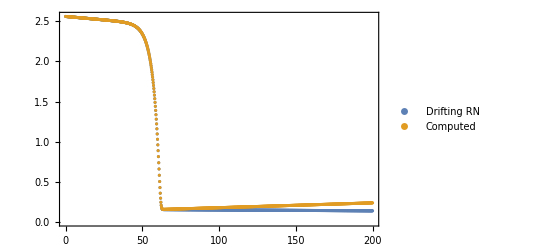

```mathematica
(* R of drifting RN versus computed R*)
endj=1000;
RNRTableU2=Table[RFromRStar[(Uvec0[[-1]]+Vvec[[j]])/2,MFunc/.{v->Vvec[[j]]},QFunc/.{v->Vvec[[j]]}]^2,{j,1,endj*skip,skip}];
ExportAndShow["R(v) RN drifting",ListPlot[{{VvecSkipped[[;;endj]],RNRTableU2}//Transpose,{VvecSkipped[[;;endj]],RTable[[;;endj,-1]]}//Transpose},Frame->True,FrameLabel->{MaTeX@"v",Rotate[MaTeX@"R",-90 Degree]},PlotLegends->{"Drifting RN","Computed"}]]
```

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than 50. digits of working precision to meet these tolerances.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of FindRoot::cvmit will be suppressed during this calculation.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of FindRoot::cvmit will be suppressed during this calculation.

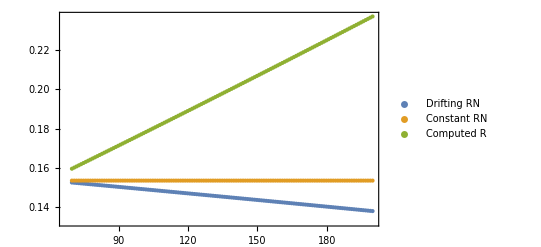

```mathematica
endj=1000;
startj=70;
skip2=5;
RNRTableU=Table[RFromRStar[(Uvec0[[-1]]+Vvec[[j]])/2,MFunc/.{v->-Uvec0[[-1]]},QFunc/.{v->-Uvec0[[-1]]}]^2,{j,1,endj*skip,skip*skip2}];
RNRTableU2=Table[RFromRStar[(Uvec0[[-1]]+Vvec[[j]])/2,MFunc/.{v->Vvec[[j]]},QFunc/.{v->Vvec[[j]]}]^2,{j,1,endj*skip,skip*skip2}];
XAxis = VvecSkipped[[startj*skip2;;endj;;skip2]];
ExportAndShow["R(v) RN drifting RN constant",ListPlot[{{XAxis,RNRTableU2[[startj;;]]}//Transpose,{XAxis,RNRTableU[[startj;;]]}//Transpose,{XAxis,RTable[[startj*skip2;;endj;;skip2,-1]]}//Transpose},PlotLegends->{"Drifting RN","Constant RN","Computed R"},Frame->True,FrameLabel->{MaTeX@"v",Rotate[MaTeX@"R",-90 Degree]}]]
```

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of FindRoot::cvmit will be suppressed during this calculation.

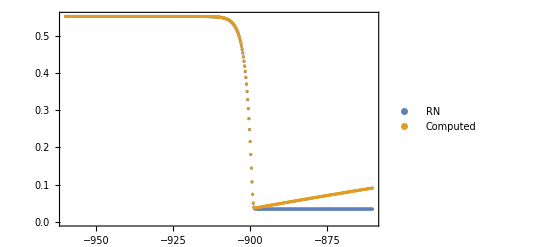

```mathematica
(*R(v=const, u) computed versus RN*)
RNRTableV=Table[RFromRStar[(Uvec0[[j]]+Vvec[[-1]])/2,MFunc/.{v->Vvec[[-1]]},QFunc/.{v->Vvec[[-1]]}]^2,{j,1,500*skip,skip}];
ExportAndShow["R(u) RN",ListPlot[{{UvecSkipped[[;;500]],RNRTableV}//Transpose,{UvecSkipped[[;;500]],RTable[[-1,;;500]]}//Transpose},PlotLegends->{"RN","Computed"},Frame->True,FrameLabel->{MaTeX@"u",Rotate[MaTeX@"R",-90 Degree]}]]
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

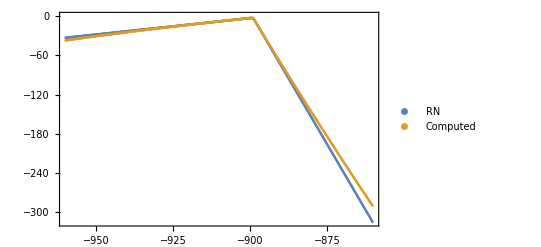

```mathematica
RNSTableU1=Log[-r f/2]/.{r->Sqrt[RTable[[-1,1;;-1;;10]]],m->MTable[[-1]],Q->QTable[[-1]]};
SApproxIndex=330;
SFinalIndex=500;
RNSTableUExact=Table[Log[-r f/2]/.{r->RFromRStar[(Uvec0[[j]]+Vvec[[-1]])/2,MFunc/.{v->Vvec[[-1]]},QFunc/.{v->Vvec[[-1]]}],m->MTable[[-1]],Q->QTable[[-1]]},{j,1,SApproxIndex*skip,skip}];
SRN=Simplify[(Log[rm/2]+Log[2κm]+Log[Δr/.Solve[rstar==RStar/.{(r-rm)->Δr}/.{r->rm},Δr][[1]]])/.{m->MTable[[-1]],Q->QTable[[-1]]}];
RNSTableUApprox=Table[SRN/.{rstar->(Uvec0[[j]]+Vvec[[-1]])/2}//N,{j,SApproxIndex*skip+1,SFinalIndex*skip,skip}];
RNSTableU=Join[RNSTableUExact,RNSTableUApprox];
ExportAndShow["S(u) RN Region2",ListPlot[{{UvecSkipped[[;;SFinalIndex]], RNSTableU}//Transpose, {UvecSkipped[[;;SFinalIndex]], STable[[-1,1;;SFinalIndex]]}//Transpose},PlotLegends->{"RN","Computed"},Frame->True,FrameLabel->{MaTeX@"u",Rotate[MaTeX@"S",-90 Degree]}]]
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

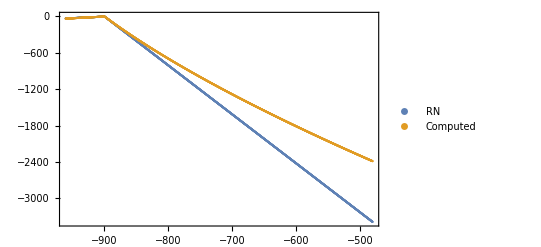

```mathematica
RNSTableU1=Log[-r f/2]/.{r->Sqrt[RTable[[-1,1;;-1;;10]]],m->MTable[[-1]],Q->QTable[[-1]]};
SApproxIndex=330;
SFinalIndex=2400;
RNSTableUExact=Table[Log[-r f/2]/.{r->RFromRStar[(Uvec0[[j]]+Vvec[[-1]])/2,MFunc/.{v->Vvec[[-1]]},QFunc/.{v->Vvec[[-1]]}],m->MTable[[-1]],Q->QTable[[-1]]},{j,1,SApproxIndex*skip,skip}];
SRN=Simplify[(Log[rm/2]+Log[2κm]+Log[Δr/.Solve[rstar==RStar/.{(r-rm)->Δr}/.{r->rm},Δr][[1]]])/.{m->MTable[[-1]],Q->QTable[[-1]]}];
RNSTableUApprox=Table[SRN/.{rstar->(Uvec0[[j]]+Vvec[[-1]])/2}//N,{j,SApproxIndex*skip+1,SFinalIndex*skip,skip}];
RNSTableU=Join[RNSTableUExact,RNSTableUApprox];
ExportAndShow["S(u) RN Region3",ListPlot[{{UvecSkipped[[;;SFinalIndex]], RNSTableU}//Transpose, {UvecSkipped[[;;SFinalIndex]], STable[[-1,1;;SFinalIndex]]}//Transpose},PlotLegends->{"RN","Computed"},Frame->True,FrameLabel->{MaTeX@"u",Rotate[MaTeX@"S",-90 Degree]}]]
```

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of FindRoot::cvmit will be suppressed during this calculation.

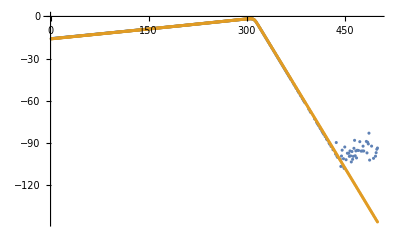

```mathematica
RNSTableV=Table[Log[-r f/2]/.{r->RFromRStar[(Uvec0[[-1]]+Vvec[[j]])/2,MFunc/.{v->Vvec[[j]]},QFunc/.{v->Vvec[[j]]}],m->MTable[[j]],Q->QTable[[j]]},{j,1,500*skip,skip}];
ListPlot[{RNSTableV, STable[[1;;500,-1]]}]
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

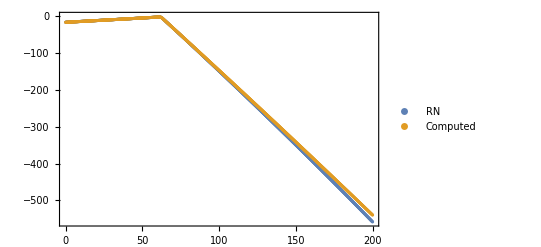

```mathematica
SApproxIndex=330;
SFinalIndex=1000;
RNSTableVExact=Table[Log[-r f/2]/.{r->RFromRStar[(Uvec0[[-1]]+Vvec[[j]])/2,MFunc/.{v->Vvec[[j]]},QFunc/.{v->Vvec[[j]]}],m->MTable[[j]],Q->QTable[[j]]},{j,1,SApproxIndex*skip,skip}];
SRN=Simplify[(Log[rm/2]+Log[2κm]+Log[Δr/.Solve[rstar==RStar/.{(r-rm)->Δr}/.{r->rm},Δr][[1]]])];
RNSTableVApprox=Table[SRN/.{rstar->(Uvec0[[-1]]+Vvec[[j]])/2, m->MTable[[j]],Q->QTable[[j]]}//N,{j,SApproxIndex*skip+1,SFinalIndex*skip,skip}];
RNSTableV=Join[RNSTableVExact,RNSTableVApprox];
ExportAndShow["S(v) RN Region2",ListPlot[{{VvecSkipped[[;;SFinalIndex]],RNSTableV}//Transpose, {VvecSkipped[[;;SFinalIndex]],STable[[1;;SFinalIndex,-1]]}//Transpose},PlotLegends->{"RN","Computed"},Frame->True,FrameLabel->{MaTeX@"v",Rotate[MaTeX@"S",-90 Degree]}]]
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

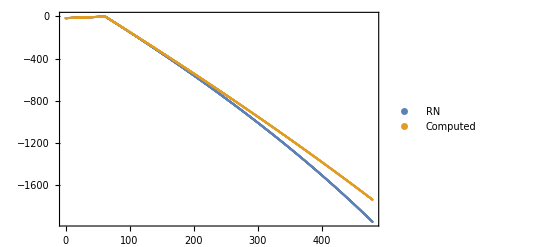

```mathematica
SApproxIndex=330;
SFinalIndex=2400;
RNSTableVExact=Table[Log[-r f/2]/.{r->RFromRStar[(Uvec0[[-1]]+Vvec[[j]])/2,MFunc/.{v->Vvec[[j]]},QFunc/.{v->Vvec[[j]]}],m->MTable[[j]],Q->QTable[[j]]},{j,1,SApproxIndex*skip,skip}];
SRN=Simplify[(Log[rm/2]+Log[2κm]+Log[Δr/.Solve[rstar==RStar/.{(r-rm)->Δr}/.{r->rm},Δr][[1]]])];
RNSTableVApprox=Table[SRN/.{rstar->(Uvec0[[-1]]+Vvec[[j]])/2, m->MTable[[j]],Q->QTable[[j]]}//N,{j,SApproxIndex*skip+1,SFinalIndex*skip,skip}];
RNSTableV=Join[RNSTableVExact,RNSTableVApprox];
ExportAndShow["S(v) RN Region3",ListPlot[{{VvecSkipped[[;;SFinalIndex]],RNSTableV}//Transpose, {VvecSkipped[[;;SFinalIndex]],STable[[1;;SFinalIndex,-1]]}//Transpose},PlotLegends->{"RN","Computed"},Frame->True,FrameLabel->{MaTeX@"v",Rotate[MaTeX@"S",-90 Degree]}]]
```

```mathematica
(*Region 3*)
```

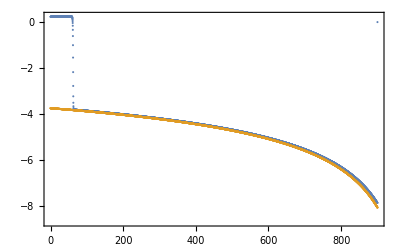

```mathematica
ExportAndShow["S,v(v) κ-",ListPlot[{{VvecSkipped,SvTable[[;;,-1]]}//Transpose,{VvecSkipped,-κm/.{m->MTable[[1;;-1;;skip]],Q->QTable[[1;;-1;;skip]]}}//Transpose},Frame->True,FrameLabel->{MaTeX@"v"},PlotLegends->MaTeX/@{"S_{,v}","-\\kappa_-^v"}]]
```

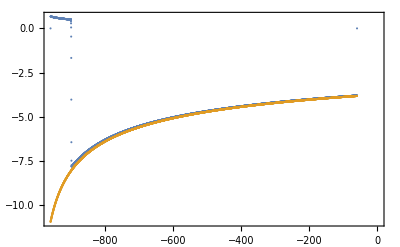

```mathematica
ExportAndShow["S,u(u) κ-",ListPlot[{{UvecSkipped,SuTable[[-1,;;]]}//Transpose,{UvecSkipped,-κm/.{m->MFunc/.{v->-Uvec0[[1;;-1;;skip]]},Q->QFunc/.{v->-Uvec0[[1;;-1;;skip]]}}}//Transpose},Frame->True,FrameLabel->{MaTeX@"u"},PlotLegends->MaTeX/@{"S_{,u}","-\\kappa_-^u"}]]
```

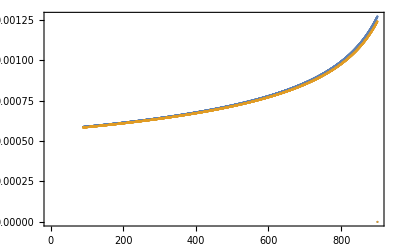

```mathematica
ExportAndShow["R,v(v) Analytical Approx",ListPlot[{{VvecSkipped[[450;;]],RvTable[[450;;,-1]]}//Transpose,{VvecSkipped[[450;;]],(-cv[[;;,-1]]/(κm/.{m->MTable[[1;;-1;;skip]],Q->QTable[[1;;-1;;skip]]}))[[450;;]]}//Transpose},Frame->True,FrameLabel->{MaTeX@"v"},PlotLegends->MaTeX/@{"R_{,v}","-\\frac{\\widetilde{T}_{vv}}{\\kappa_{-}^{v}}"}]]
```

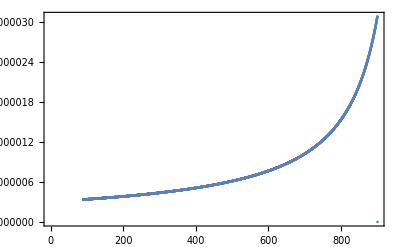

```mathematica
ExportAndShow["R,v(v)-Analytical Approx",ListPlot[{VvecSkipped[[450;;]],RvTable[[450;;,-1]]-(-cv[[;;,-1]]/(κm/.{m->MTable[[1;;-1;;skip]],Q->QTable[[1;;-1;;skip]]}))[[450;;]]}//Transpose,Frame->True,FrameLabel->{MaTeX@"v",Rotate[MaTeX@"R_{,v}+\\frac{\\widetilde{T}_{vv}}{\\kappa_{-}^{v}}",-90 Degree]}]]
```

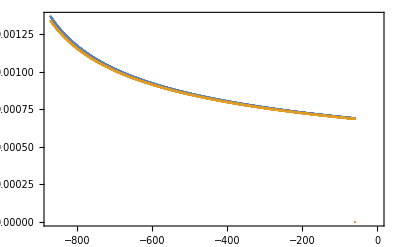

```mathematica
ExportAndShow["R,u(u) Analytical Approx",ListPlot[{{UvecSkipped[[450;;]],RuTable[[-1,450;;]]}//Transpose,{UvecSkipped[[450;;]],(-cu[[-1,;;]]/(κm/.{m->MFunc/.{v->-Uvec0[[1;;-1;;skip]]},Q->QFunc/.{v->-Uvec0[[1;;-1;;skip]]}}))[[450;;]]}//Transpose},Frame->True,FrameLabel->{MaTeX@"v"},PlotLegends->MaTeX/@{"R_{,u}","-\\frac{\\widetilde{T}_{uu}}{\\kappa_{-}^{u}}"}]]
```